### Start choosing the example:

```mathematica
t=11;
beta = 0;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
A=0.2;
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

```mathematica
Data["Switching Costs"]={};
```

#### This was taking around 40 min.... Now it just takes seconds!

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U2-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 4.58467 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{5.11873,Null}

```mathematica
Reduce[j498==1.&&j499==0&&j508==0&&jt511==0&&jt517==0&&1. jt524==1.&&jt527==0&&jt531==0&&u535==2.&&1. u536==2.&&u537==1.&&u538==1.&&u539==1.&&1. u541==2.&&(j501==1.||1. j501==1.)]
```

j501==1.&&u541==2.&&u539==1.&&u538==1.&&u537==1.&&u536==2.&&u535==2.&&jt531==0.&&jt527==0.&&jt524==1.&&jt517==0.&&jt511==0.&&j508==0.&&j499==0.&&j498==1.

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j69→2.-1. j70+1. j71-1. j73+1. j80-1. jt100+1. jt83+1. jt96,j72→2.-1. j73+1. j80+1. jt103,j74→2.,j75→2.,j76→0.+1. jt83,j77→0.+1. j71-1. j73+1. j80-1. jt100+1. jt96,j78→0.+1. j70+1. jt100-1. jt96,j79→0.+1. jt103,j81→0.,j82→0.,jt101→0.+1. j80,jt102→2.-1. j73+1. jt103,jt104→0.+1. j73-1. jt103,jt105→0.,jt106→0.,jt84→0.,jt85→0.+1. j71-1. j73+1. j80-1. jt100+1. jt96,jt86→0.,jt87→2.-1. j70+1. jt83,jt88→0.+1. j70-1. jt83,jt90→2.-1. j70+1. j71-1. j73+1. j80-1. jt100+1. jt83-1. jt89+1. jt96,jt91→0.+1. j71-1. jt103+1. jt83-1. jt89,jt92→0.+1. j70-1. j71+1. jt100+1. jt103-1. jt83+1. jt89-1. jt96,jt93→0.-1. j71+1. jt103+1. jt89,jt94→0.+1. j71-1. jt89,jt95→0.+1. j70-1. jt96,jt97→0.+1. j71-1. j73+1. jt96,jt98→0.+1. j73-1. jt96,jt99→0.+1. j80-1. jt100,u112→0.,u114→-2.+1. j70-1. j71+1. j73-1. j80+1. jt100-1. jt96+1. u107,u115→0.-1. j70+1. j71-1. j73+1. j80-1. jt100+1. jt96+1. u108,u116→0.+1. j70-1. j71+1. jt100-1. jt96+1. u109,u117→-2.+1. j73-1. j80+1. u110,u118→0.-1. j73+1. j80+1. u111,u119→0.,u120→0.+1. u113|>

```mathematica
MFGEquations["EqAllAll"]/.%20//Simplify
```

$Aborted

#### Non-linear case

```mathematica
alpha = 0;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

{10.3609,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→1.41151,u4210→1.41151,u4211→0.705756,u4212→0.705756,u4213→0.705756,u4214→0.,u4215→1.41151,u4216→0.705756,u4217→0.705756,u4218→0.705756,u4219→0.,u4220→0.,u4221→0.,u4222→1.41151|>}

```mathematica
alpha = 0.1;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

{9.85946,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→1.4537,u4210→1.4537,u4211→0.72685,u4212→0.72685,u4213→0.72685,u4214→0.,u4215→1.4537,u4216→0.72685,u4217→0.72685,u4218→0.72685,u4219→0.,u4220→0.,u4221→0.,u4222→1.4537|>}

```mathematica
alpha = 0.3;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

{9.71554,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→1.54642,u4210→1.54642,u4211→0.773209,u4212→0.773209,u4213→0.773209,u4214→0.,u4215→1.54642,u4216→0.773209,u4217→0.773209,u4218→0.773209,u4219→0.,u4220→0.,u4221→0.,u4222→1.54642|>}

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→1.9184,u4210→1.9184,u4211→0.959201,u4212→0.959201,u4213→0.959201,u4214→0.,u4215→1.9184,u4216→0.959201,u4217→0.959201,u4218→0.959201,u4219→0.,u4220→0.,u4221→0.,u4222→1.9184|>

```mathematica
alpha = 1;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.22045×10^-15,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.22045×10^-15,ComplexInfinity]

{9.17299,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.,u4210→2.,u4211→1.,u4212→1.,u4213→1.,u4214→0.,u4215→2.,u4216→1.,u4217→1.,u4218→1.,u4219→0.,u4220→0.,u4221→0.,u4222→2.|>}

```mathematica
alpha = 1.2;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

{9.98287,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.1882,u4210→2.1882,u4211→1.0941,u4212→1.0941,u4213→1.0941,u4214→0.,u4215→2.1882,u4216→1.0941,u4217→1.0941,u4218→1.0941,u4219→0.,u4220→0.,u4221→0.,u4222→2.1882|>}

```mathematica
alpha = 1.5;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

{9.96328,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.55799,u4210→2.55799,u4211→1.27899,u4212→1.27899,u4213→1.27899,u4214→0.,u4215→2.55799,u4216→1.27899,u4217→1.27899,u4218→1.27899,u4219→0.,u4220→0.,u4221→0.,u4222→2.55799|>}

```mathematica
alpha = 1.6;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

{9.94994,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.71476,u4210→2.71476,u4211→1.35738,u4212→1.35738,u4213→1.35738,u4214→0.,u4215→2.71476,u4216→1.35738,u4217→1.35738,u4218→1.35738,u4219→0.,u4220→0.,u4221→0.,u4222→2.71476|>}

```mathematica
alpha = 1.6001;
(FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

{10.0769,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.71493,u4210→2.71493,u4211→1.35746,u4212→1.35746,u4213→1.35746,u4214→0.,u4215→2.71493,u4216→1.35746,u4217→1.35746,u4218→1.35746,u4219→0.,u4220→0.,u4221→0.,u4222→2.71493|>}

```mathematica
alpha = 1.605;
(FFR=FixedPoint[FixedReduceX1[MFGEquations],FFR,10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

{9.98061,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.72317,u4210→2.72317,u4211→1.36159,u4212→1.36159,u4213→1.36159,u4214→0.,u4215→2.72317,u4216→1.36159,u4217→1.36159,u4218→1.36159,u4219→0.,u4220→0.,u4221→0.,u4222→2.72317|>}

```mathematica
alpha = 1.605;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

{9.84627,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.72317,u4210→2.72317,u4211→1.36159,u4212→1.36159,u4213→1.36159,u4214→0.,u4215→2.72317,u4216→1.36159,u4217→1.36159,u4218→1.36159,u4219→0.,u4220→0.,u4221→0.,u4222→2.72317|>}

```mathematica
alpha = 1.61;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

{9.96503,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.73164,u4210→2.73164,u4211→1.36582,u4212→1.36582,u4213→1.36582,u4214→0.,u4215→2.73164,u4216→1.36582,u4217→1.36582,u4218→1.36582,u4219→0.,u4220→0.,u4221→0.,u4222→2.73164|>}

```mathematica
alpha = 1.62;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

{9.91102,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.74876,u4210→2.74876,u4211→1.37438,u4212→1.37438,u4213→1.37438,u4214→0.,u4215→2.74876,u4216→1.37438,u4217→1.37438,u4218→1.37438,u4219→0.,u4220→0.,u4221→0.,u4222→2.74876|>}

```mathematica
alpha = 1.65;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

{9.90551,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.8016,u4210→2.8016,u4211→1.4008,u4212→1.4008,u4213→1.4008,u4214→0.,u4215→2.8016,u4216→1.4008,u4217→1.4008,u4218→1.4008,u4219→0.,u4220→0.,u4221→0.,u4222→2.8016|>}

```mathematica
alpha = 1.7;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

{9.9481,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→2.89499,u4210→2.89499,u4211→1.4475,u4212→1.4475,u4213→1.4475,u4214→0.,u4215→2.89499,u4216→1.4475,u4217→1.4475,u4218→1.4475,u4219→0.,u4220→0.,u4221→0.,u4222→2.89499|>}

```mathematica
alpha = 1.8;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.01914×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.01914×10^-16

{9.8611,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→3.10493,u4210→3.10493,u4211→1.55247,u4212→1.55247,u4213→1.55247,u4214→0.,u4215→3.10493,u4216→1.55247,u4217→1.55247,u4218→1.55247,u4219→0.,u4220→0.,u4221→0.,u4222→3.10493|>}

```mathematica
alpha = 1.9;
(FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort)//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.01872×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.01872×10^-16

{9.90964,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→3.3534,u4210→3.3534,u4211→1.6767,u4212→1.6767,u4213→1.6767,u4214→0.,u4215→3.3534,u4216→1.6767,u4217→1.6767,u4218→1.6767,u4219→0.,u4220→0.,u4221→0.,u4222→3.3534|>}

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort//AbsoluteTiming
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.28965×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.28965×10^-16

{9.65963,<|j4171→1.,j4172→1.,j4173→0.,j4174→1.,j4175→1.,j4176→2.,j4177→2.,j4178→0.,j4179→0,j4180→0,j4181→0,j4182→0,j4183→0.,j4184→0.,jt4185→0.,jt4186→0.,jt4187→0.,jt4188→0.,jt4189→1.,jt4190→1.,jt4191→0.,jt4192→1.,jt4193→0.,jt4194→0.,jt4195→0,jt4196→0.,jt4197→0.,jt4198→1.,jt4199→0.,jt4200→0.,jt4201→0,jt4202→0.,jt4203→0.,jt4204→1.,jt4205→0.,jt4206→1.,jt4207→0.,jt4208→0.,u4209→3.65335,u4210→3.65335,u4211→1.82668,u4212→1.82668,u4213→1.82668,u4214→0.,u4215→3.65335,u4216→1.82668,u4217→1.82668,u4218→1.82668,u4219→0.,u4220→0.,u4221→0.,u4222→3.65335|>}

### What we this plot for?

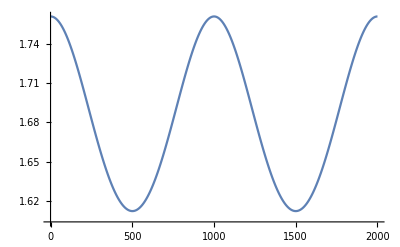

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.